# MMA notes

Yiming Ma

Personal Mathematica notes.

## 格式前置

Set the outline box:

```mathematica
SetOptions[EvaluationNotebook[], DockedCells->{Cell[BoxData[ToBoxes[ResourceFunction["NotebookOutlineMenu"][EvaluationNotebook[]]]]]}]
```

Clear all $Context variables:

```mathematica
ClearAll/@(($Context<>"*")//Names);
```

## MMA 基本概念

MMA 编程范式:

procedural (C-like). 最佳实践几乎一定不是 procedural way.

functional

rule-based

### Expression

在 MMA 中, 一切皆为 expression . Expression . 所有的 normal expression 都可以分解为三部分 : 1. atoms (包括 symbol, number,  string), 2. 方括号 [], 3. 逗号。

atom中的 symbol, 由字母, 数字和 $ 符号组成。所有 system-defined symbol, 要么以大写字母开头, 要么以 $ 开头 (e.g. Plus, D, FullForm, $Version, $MachinePrecision)。所以自定义的 symbol 应该永远以小写字母开头。

atom中的number, 分为四类, integer (like dddd, Integer), real number (like ddd.ddd, Real), rational number (like integer1/integer2, Rational), complex number (like a+b I, 其中 a 和 b 是任意其它三类 number, Complex)

atom中的 string (String), 是由 “” 包住的字符串, 如果想在字符串中输入双引号 “ ，那么用转义字符就可以了: \”。

如果表面上看起来表达式的组成不是 symbol + atom + , MMA 也会在内部解析为以上三部分。比如，a*a 会解析为 Times[a,a], a^3 会解析为 Power[a,3] 之类的，而所谓的 *, +,- 都是 special input form. 如果想看到MMA 是怎么看待 normal expression的，可以使用 FullForm[] 函数

```mathematica
FullForm[4*a^2]
```

Times[4,Power[a,2]]

MMA 在求解 expression 的时候, 首先会将 expression 转换为基本的 FullForm 形式, 求解顺序是从树底向上求解, 求解了一部分分支, 就把原来的分支替换为求解结果生成一个更小的树, 这样一直循环往复得到最后的结果。 如果想看一个 expression 的 tree, 就用 TreeForm 这个函数

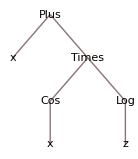

```mathematica
TreeForm[x+Cos[x]*Log[z]]
```

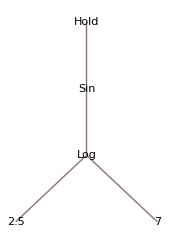

```mathematica
TreeForm[Hold[Sin[Log[2.5,7]]]](*注意了这里要使用 Hold. Hold 的作用是避免 evaluate expression *)
```

Another very import conception is level. level 0 means the entire expression, level 1 removes one layer, level 2 removes two layers and so on. We can use Position to get the position of a element in the list. If the Position function returns a list contains 2 integers like {1,1}, it means the position in {level1, level2}.

```mathematica
alist = {{a,b},{c,{d,e}}};
```

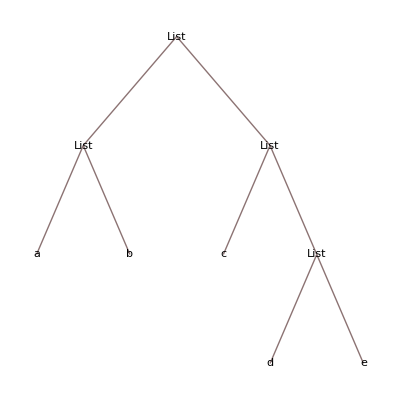

```mathematica
alist // TreeForm
```

```mathematica
Level[alist,{1}]
```

{{a,b},{c,{d,e}}}

```mathematica
Level[alist,{2}]
```

{a,b,c,{d,e}}

```mathematica
Level[alist,{3}]
```

{d,e}

```mathematica
Position[alist,d]
```

{{2,2,1}}

```mathematica
MapAt[f,alist,{2,2,1}]
```

{{a,b},{c,{f[d],e}}}

### 基本语法

运算符

+ (addition), - (subtraction), * (multiplication), \ (division), ^ (exponentiation), +=, -=, *=, /=

>  (Greater), != (Unequal), && (And), <= (LessEqual), || (Or), == (Equal)

对于不可 evaluate 的 symbol, 有: === (SameQ) 和 =!= (UnsameQ)

结果

% (上一次运行的输出)

%%... (n个 %, 上 n 次运行的输出) 等价于 %n 或 Out[n]

赋值

lhs = rhs (Set, 把赋值的那一刻, 把 rhs evaluate 之后的值给 lhs )

lhs := rhs (SetDelayed, 在赋值的那一刻不立即 evaluate rhs)

函数

@ (Prefix, e.g. f @ x,  Prefix 只适用于单一 argument 的函数, 纯粹是为了省去括号[], 没有更多的语义)

/@ (Map, e.g. f /@ {a, b, c} 等价于{f[a], f[b], f[c]}. 对于没有 listable attribute 的 symbol, 相当于免去了定义 listable 属性的麻烦 )

@@ (Apply, e.g. f@@{a,b,c} means f[a,b,c])

pure function, like Power @@ # &, #(slot) means formal variable and & terminates the pure function. We can also use #1, #2 ....

// (Postfix, e.g. x // f)

x~f~y (Infix)

优先级: Prefix > Infix > Postfix, 不过不用记忆, 养成加 () 的好习惯

f[x_,y_]:= expr (_ 叫做 Blank)

f[x_,y_]:=(firstLine; secondLine; ... lastLine)  (这种写法叫做 compound expression, 即不同的 expression 之间用 ; 隔开)

MMA 中不允许在函数内修改函数的 parameter, 原因是, MMA 在调用函数的时候所有的参数都会被 evaluated 然后替换掉函数中所有出现参数的地方。

Attributes 查看一个函数的 attribute

Rule

a->b (rule 的形式)

/. (即ReplaceAll[expr, rule] )

//. (即 ReplaceRepeated[rules])

Options[symbol] (查看 symbol (通常是函数的名字) 的option, 这些option 都是以 rule 的形式展示的, 看到隐藏的options可以去修改)

SetOptions[symbol, option]

=. (即 Unset 一个 rule, 清除 =. lhs 的 rule, 比如 f[x_]=. , 就是清除 f[x_] 的 DownValues, 但 f[x_Integer] 的定义还会在 DownValues[f] 中保留; f=. 就是清除 f 的 OwnValues)

pattern:value, pattern with default value, 比如 x_:2 .

_. 代表着一个默认为 0 的可以不输入的 pattern, 比如 f[x_, y_.] .

__ (BlankSequence, 代表一个或多个 pattern, 不同 pattern 用 , 隔开 )

___ (BlankNullSequence, 代表 0 个或多个 pattern, 不同 pattern 用 , 隔开)

_head ( pattern constraints, 规定只有 Head 是 head 的才匹配)

_?test (pattern constraints, test 是一个只返回 True 或 False 的函数 symbol, 只匹配 test 函数输出为 True 的 pattern)

pattern /; test (condition, condition 后面跟一个只范围 True 或 False 的函数 test, 只匹配 test 函数输出为 True 的 pattern)

name:pattern (给 pattern 起名为 name 的别名, 和 n_ 类似, 好处是后面跟的 pattern 可以足够复杂 )

pattern.. (重复了1次或多次的 pattern )

pattern... (重复了 0 次或多次的 pattern)

pattern1 | pattern2 (满足 pattern1 或者 满足 pattern2)

^:= (UpSetDelayed, 用来设置函数中 arguments 的 UpValues)

/: ... := (TagSetDelayed, 一种更好的设置函数中 arguments 的 UpValues 的方法)

Information

?symbol (查看这个 symbol 的information)

??symbol (查看这个 symbol 的 more detailed information)

?*Solve* (模糊查找 symbol 的name)

List

TableForm[list], MatrixForm[list] (用来展示 list, 两者差不多, 区别是 MatrixForm 的列宽是相等的)

[[ ]] (Part, 提取元素)

### List 和 String

#### list 基本定义

a sequence of expressions

```mathematica
list1 = {a, N[Pi], Sqrt[3]} 
list2={list1, {d,{e,f}}}
```

{a,3.14159,√3}

{{a,3.14159,√3},{d,{e,f}}}

#### 展示 list

```mathematica
TableForm[{list1, {d,e,f}}]
```

a | 3.14159 | √3
d | e | f

```mathematica
MatrixForm[{list1, {d,e,f}}]
```

(a | 3.14159 | √3
d | e | f)

#### 提取元素

```mathematica
list1[[3]]
```

√3

```mathematica
list1[[{3,2}]] (*提取第3个和第2个元素*)
```

{√3,3.14159}

```mathematica
list2[[1,2]](*提取第1个元素中的第2个元素*)
```

3.14159

#### 产生list

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[4,12,2]
```

{4,6,8,10,12}

Array[function, n] 也很好用, n 是个数的意思

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

最最常用的是 Table[expression, {variable, start, end, step}]

```mathematica
Table[i,{i,1,10,1}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[Prime[i],{i,1,10,1}]
```

{2,3,5,7,11,13,17,19,23,29}

#### Listable function

MMA 中所有的内置的和数值计算相关的函数 (numerical functions, e.g. Plus, Sin, Gamma), 和作判定有关的函数 (predicates, e.g. IntegerQ, PrimeQ) 以及部分的操作符号的函数 (symbolic functions, e.g. Together, ToExpression), 都具有 Listable 的属性, 对于一个具有 Listable 属性的函数, f[{list}] 相当于 {f[list[[1]]], f[list[[2]]] ...}

```mathematica
Attributes[Sqrt]
```

{Listable,NumericFunction,Protected}

```mathematica
Sqrt[{a,b,c}]
```

{√a,√b,√c}

```mathematica
{a,b,c}^d
```

{a^d,b^d,c^d}

```mathematica
a^{d,e,f}
```

{a^d,a^e,a^f}

如果是自定义的函数, 也可以赋值给它 Listable 的 attribute:

```mathematica
greater2[x_]:=x>2;
greater2[{1,2,3}]
```

{1,2,3}>2

```mathematica
greater2/@{1,2,3}
```

{False,False,True}

```mathematica
SetAttributes[greater2,Listable]
```

```mathematica
greater2[{1,2,3}]
```

{False,False,True}

注意了! 如果想要删除函数, 只是 Clear 只能删除函数的 definition, 但是无法删除 attributes. 想要彻底删除要用 ClearAll.

常用的展示 list 属性的函数

```mathematica
Length[{a,b,c}]
```

3

```mathematica
Dimensions[{{a,b,c}, {d,e,f}}]
```

{2,3}

```mathematica
MemberQ[{a,b,c},d]
```

False

```mathematica
Count[{a,b,c,a},a]
```

2

```mathematica
Position[{a,b,{a,c}},a]
```

{{1},{3,1}}

predicate (断言), 就是 *Q 函数, 用来判断 expression 是否具有某种属性, 然后只返回 True 或 False.和列表结合起来, 常用函数如下:

```mathematica
Select[{a,1.1, 2, 3, 4.5},IntegerQ]
```

{2,3}

```mathematica
{VectorQ[{a,b,c}],VectorQ[{a,b,{a,b}}]}
```

{True,False}

```mathematica
?*Q
```

#### 操作 List

当我们操作 List 的时候, 只有 AppendTo 和 PrependTo 两个函数会覆写原来的 List, 其它的所有操作均是在原有 List 的 copy 上作修改。

```mathematica
list3= {a,b,c,d,e};
```

```mathematica
Append[list3, 42]
```

{a,b,c,d,e,42}

```mathematica
Prepend[list3,{x,y}]
```

{{x,y},a,b,c,d,e}

```mathematica
Insert[list3,Pi,4]
```

{a,b,c,π,d,e}

```mathematica
list3
```

{a,b,c,d,e}

```mathematica
AppendTo[list3, 42]
```

{a,b,c,d,e,42}

```mathematica
PrependTo[list3,{x,y}]
```

{{x,y},a,b,c,d,e,42}

```mathematica
list3
```

{{x,y},a,b,c,d,e,42}

```mathematica
ReplacePart[list3,new,1]
```

{new,a,b,c,d,e,42}

```mathematica
Take[list3,{2,4}] (*连续提取元素*)
```

{a,b,c}

```mathematica
Drop[list3,{2,4}] (*连续丢弃元素*)
```

{{x,y},d,e,42}

#### 操作 String

常用的函数和 List 的函数很像。比如 StringLength, StringPosition, StringQ, LetterQ, DigitQ, StringMatchQ, StringTake, StringDrop, StringInsert 等等.

```mathematica
StringJoin["Hello", " World", "!"]
```

Hello World!

```mathematica
"Hello"<> " World" <>"!"  (* <> 是 StringJoin 的简写*)
```

Hello World!

```mathematica
ToExpression["a+b"]
```

a+b

## 函数

MMA 本质上是一种函数式的语言。函数式意味着, 函数和数据没有区别: 函数可以被当作数据一样去处理, 在函数之间传递。

所谓的函数, 其实就是一种 global 的 rule, 可以用 DownValues 去查看这个 rule 具体长什么样子。

MMA 的 kernel 叫做 infinite evaluation system, 它的逻辑其实就是: expression //. {all global rules} . 如果说 rules 的逻辑中有包含关系, 比如遇到了 function overloading 的情况, 用户定义了 f[0] 怎么办以及 f[x_Integer] 怎么办, 那么 MMA 在解释的时候永远优先使用 more specific rules, 比如, 如果输入 argument 是 0 的话优先使用 f[0] 的定义。

```mathematica
ClearAll/@(($Context<>"*")//Names);
```

### 数据类型

每一个表达式都有一个 Head, 这个 Head 就是这个表达式的 type.

```mathematica
Head/@{3,3/2,3+2*I,{3,2},a}
```

{Integer,Rational,Complex,List,Symbol}

在定义函数的时候, 我们有时候需要类型检查 :

```mathematica
fact[n_Integer]:=Product[i,{i,n}];
```

```mathematica
fact[4]
```

24

```mathematica
fact[3.5]
```

fact[3.5]

也可以定义函数时候, 限定多种数据类型:

```mathematica
squareAnyNumber[n_Integer|n_Real|n_Rational|n_Complex|n_List]:=n^2;
```

```mathematica
squareAnyNumber/@{3, 4.5, 2/3,3+4*I,{1,2,3},x}
```

{9,20.25,4/9,-7+24 ⅈ,{1,4,9},squareAnyNumber[x]}

### Module

如果函数稍微复杂一些, 就需要定义 local variable. 如果想要避免函数里面的中间过程的变量泄露到全局的 context 里, 就要使用 Module.

```mathematica
quad[a_,b_,c_]:=
Module[
{d},
d=Sqrt[b^2-4*a*c];
{-b+d,-b-d}/(2*a)
]
```

```mathematica
{quad[1,1,1],d}
```

{{1/2 (-1+ⅈ √3),1/2 (-1-ⅈ √3)},d}

或者也可以在 Module 里面定义多个变量:

```mathematica
Clear[quad]
quad[a_,b_,c_]:=
Module[
{d = Sqrt[b^2-4*a*c],e=2*a},
{-b+d,-b-d}/e
]
```

```mathematica
quad[1,0,-16]
```

{4,-4}

除了 Module, 还可以使用 With. With 里面, With[{name=expr},body] 中的 name 不再是变量, 而是类似于 C 语言里面 #define 的宏定义, 它会把出现 name 的地方都替换成 expr, 所以 name 被第一次定义之后也无法被再次赋值。优点: faster than Module.

```mathematica
Clear[quad]
quad[a_,b_,c_]:=
With[
{d=Sqrt[b^2-4*a*c],e=2*a},
{-b+d,-b-d}/e
]
```

```mathematica
quad[1,0,-16]
```

{4,-4}

#### 条件

在 MMA 中, 即使是 If, Switch, Which (Which 和 if...elif...else 的效果是一样的) 之类的, 也不是语法中的关键字, 而是作为函数出现, 这是MMA本质上是函数式编程的一种体现。

MMA中的条件函数 (Conditional execution), 主要有 If, Switch, Which, Do, For, While.

### 花样映射

除了MapAt, 还有很多其他的映射，比如 MapThread 相当于让一个函数作用于矩阵的每一列:

```mathematica
MapThread[f,{{a1,a2},{b1,b2},{c1,c2}}]
```

{f[a1,b1,c1],f[a2,b2,c2]}

除了 MapThread, 还有 Thread, Tread 可以作用于多个 list 和 scalar, scalar 是公共的部分, list 组成矩阵, 并且 Thread 作用于矩阵的每一列:

```mathematica
Thread[f[{a1,b1},{b1,b2},c]]
```

{f[a1,b1,c],f[b1,b2,c]}

```mathematica
Thread[Equal[{1,2,3},{1,2,6}]](*因为Thread函数总是先执行它的 argument, 所以这里得不到想要的答案, 为了解决这个问题, 可以使用 Unevaluated*)
```

False

```mathematica
Thread[Equal[{1,2,3},{1,2,6}]//Unevaluated]
```

{True,True,False}

如果说 Thread 的作用是让一个函数作用于多个list, 那么 Through 函数就是让多个函数作用于单个 list:

```mathematica
Through[{f,g,h}[a,b,c]]
```

{f[a,b,c],g[a,b,c],h[a,b,c]}

在矩阵操作的时候, 我们通常需要知道矩阵元素的 index, 以及对应 index 的 value, 然后基于 index + value 来操作矩阵元素。通常的做法是写 for 循环。在 MMA 中, 这一个操作可以被函数替代，就是 MapIndexed:

```mathematica
MapIndexed[f,{a,b,c}]
```

{f[a,{1}],f[b,{2}],f[c,{3}]}

MapIndexed 在操作的时候, 会让函数同时作用于 value 和 value 的 position! 这个特别有用。

```mathematica
MapIndexed[f,{{a,b,c},{d,e}}] (*作用于 level 1 *)
```

{f[{a,b,c},{1}],f[{d,e},{2}]}

```mathematica
MapIndexed[f,{{a,b,c},{d,e}},{2}] (*作用于 level 2*)
```

{{f[a,{1,1}],f[b,{1,2}],f[c,{1,3}]},{f[d,{2,1}],f[e,{2,2}]}}

```mathematica
diagQ[m_]:=Module[{},
(*非对角元素都是0, 对角元素直接置 True *)
MapIndexed[((#1==0) && (Unequal@@#2)) || (Equal@@#2) &,m,{2}]//Flatten//And@@#&
];
```

```mathematica
diagQ[{{1,0},{0,1}}]
```

True

```mathematica
diagQ[{{1,0},{1,1}}]
```

False

### 用于迭代的函数

用于迭代的函数, 通常可以用来取代过程式编程中的 loop.

当我们想让一个函数反复作用于输出时, 我们可以用:

```mathematica
Nest[1/(1+#)&,x,3]
```

1/(1+1/(1+1/(1+x)))

```mathematica
NestList[1/(1+#)&,x,3]
```

{x,1/(1+x),1/(1+1/(1+x)),1/(1+1/(1+1/(1+x)))}

用于求迭代时, 常用的是 FixedPoint, 第一个 argument 被迭代的expression, 一直迭代到 expression 不变为之; 第二个 argument 是 initial value :

```mathematica
FixedPoint[(#+2/#)/2&,1.]
```

1.41421

```mathematica
FixedPointList[(#+2/#)/2&,1.]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421}

### Option

函数是可以有 Option 的, 所谓的函数的 Option, 其实就是一种为 rule 的 argument (包括 Rule name -> value 和 RuleDelayed name :> value)

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

OptionQ 可以查看一个函数是否有 options,

```mathematica
Cases[{f[x],f[x,a->b], f[x,a:>b, c->d],f[x,{a->b,c->d},e->f]}, f[arg1_, opts___?OptionQ]->{opts}]
```

{{},{a→b},{a:>b,c→d},{{a→b,c→d},e→f}}

```mathematica
f[x_,a->b]:=x;
```

```mathematica
f[a]
```

f[a]

### Attribute

对于内置的函数, 我们是没办法覆写的，原因是内置的函数都具有 Protected 的 attribute:

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

如果想要 overwrite built-in function, 要先 Unprotect 一个函数, 重新定义函数, 然后最好重新 Protect 新定义的函数。

当然, 也有一类 symbol 是绝对不允许修改的, 它们具有属性 Locked:

```mathematica
Attributes[List]
```

{Locked,Protected}

复写函数的另一种方式, 是使用 upvalue, ^:= 是 UpSetDelayed, 用来定义 UpValues:

```mathematica
Attributes[Protect]
```

{HoldAll,Protected}

```mathematica
Clear[log]
```

```mathematica
Factor[log[x_*y_]]^:=log[x]+log[y];
```

```mathematica
{DownValues@Factor, UpValues@Factor}
```

{{},{}}

```mathematica
{DownValues@log, UpValues@log}
```

{{},{HoldPattern[Factor[log[x_ y_]]]:>log[x]+log[y]}}

可以从上面的例子体会到什么是 UpValues,  DownValues 是绑定在 symbol 上的一系列 rules, 当检查这个 symbol 所绑定的 rule 的时候, 是从这个作为 Head 的  symbol 以下开始查找 rule; 如果是 UpValues, 那么当这个 symbol 作为 Head 的时候, 检查 rule 是向上检查的, 即检查这个被调用的 symbol 是不是嵌套于某种 pattern 之中。总而言之，作为 DownValues 的 rule, 自己是 pattern 的 Head; 作为 UpValues 的 rule, 自己是 pattern 里面的一部分。

```mathematica
Factor[log[(x+2)*(x+5)]]
```

log[2+x]+log[5+x]

另外一种更好的绑定 UpValue? 的方式是使用 TagSetDelayed (/: ... :=)

```mathematica
log/:Factor[log[x_*y_]]:=log[x]+log[y];
```

TagSetDelayed 绑定 UpValues 的好处是什么呢? 对于具有多个 arguments 的函数, 使用 UpSetDelayed 的时候,  f[g[x_], h[y_,z_], i]^:= ,所有的 arguments 都会拥有 UpValues, 即 g,h,i 都有了 UpValues. 但如果使用 TagSetDelayed, 就可以指定特定的 arguments 具有 UpValues.

## Rule and pattern

### pattern

什么是 pattern? 所谓的 pattern, 就是一类 expression 的总称, pattern 自己也是 expression。pattern 一般都以 Blank 结尾, 比如 xxx_. 最简单的 pattern 就是 Blank 自己 _, 代表任何 expression. 也有的 pattern 写作 xxx_f, 意思是以 f 作为 Head 的 expression. 带有 -> 的就是 rule. 用 rule 的好处就是, 你可以在定义函数的时候一直加 rule 上去!!!!

```mathematica
3*a + 4.5*b^2 /.x_Real -> x^2
```

3 a+20.25 b^2

```mathematica
3*a + 4.5*b^2 /.x_Symbol -> x^2 (*Symbol 的概念实在是太广了, 毕竟*)
```

Plus^2[Times^2[3,a^2],Times^2[4.5,Power^2[b^2,2]]]

```mathematica
(f[a]+f[b])/f[a,b]/.x_f->x^2 (* Head 是 f 的表达式 x 都替换成 x^2 *)
```

(f[a]^2+f[b]^2)/f[a,b]^2

```mathematica
(f[a]+f[b])/f[a,b]/.f[x_]->x^2
```

(a^2+b^2)/f[a,b]

```mathematica
f[a]+g[b] /.x_[a_]->a  (* destructing *)
```

a+b

```mathematica
f[a]+g[b]/.x_[_,_]->x
```

Plus

```mathematica
f[a] + g[b] /.x_[y_]->y[x]
```

a[f]+b[g]

```mathematica
(*这个厉害了*)
data  = {{x1,y1}, {x2, y2},{x3,y3}, {x4,y4}};
data /.{x_,y_}->{x,Log[y]}
```

{{x1,Log[y1]},{x2,Log[y2]},{x3,Log[y3]},{x4,Log[y4]}}

```mathematica
data
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}

```mathematica
(*这个更厉害了!*)
```

```mathematica
expandrule=x_*(y_+z_)->x*y+x*z;
```

```mathematica
FixedPoint[#/.expandrule&,a*(b+c)*(d+e+f)]  (*反复替代直到收敛*)
```

a b d+a c d+a b e+a c e+a b f+a c f

```mathematica
a*(b+c)*(d+e+f)//.expandrule  (* 还可以使用 //. !!! *)
```

a b d+a c d+a b e+a c e+a b f+a c f

#### 设定 pattern 的默认值

设定 pattern 默认值的形式为: pattern:value .

```mathematica
Clear[f,a,b,c]
Cases[{f[x,y,z], f[x,y], f[x]}, f[a_,b_:2,c_:3]->{a,b,c}]
```

{{x,y,z},{x,y,3},{x,2,3}}

#### 匹配多个表达式

匹配1 个或多个多个 pattern 用 BlankSequence (__, double blank) , 匹配 0 个或多个 pattern 用 BlankNullSequence (___, triple blank), 不同的 pattern 之间用 comma , 隔开。也可以理解为, __ 可以代表 1 个以及多个 pattern, ___ 代表着 0 个或多个 pattern.

```mathematica
Clear[f]
```

```mathematica
Cases[{f[], f[1], f[1,2]}, f[__]]
```

{f[1],f[1,2]}

```mathematica
Cases[{f[], f[1], f[1,2]}, f[___]]
```

{f[],f[1],f[1,2]}

```mathematica
Cases[{f[1,2,3], f[1,a,3]}, f[__?IntegerQ]]
```

{f[1,2,3]}

#### pattern 的别名

给 pattern 起名字, 既可以是 n_ (pattern 的名字是 n), 也可以是 name:pattern, 区别是 name:pattern 的形式中 pattern 可以足够复杂

```mathematica
Cases[{{1,2,3},a,{4,5}},t:{__Integer}->t^2]
```

{{1,4,9},{16,25}}

#### pattern 的重复

pattern.. 代表重复了 1 次或多次的 pattern, pattern... 代表重复了 0 次或多次的 pattern

有一个我不是很能想明白的例子, 只能大概看懂, 但感觉很神奇. 如果想构造一个 enCode 函数, 读取一个 list, 返回 list 中每个整数分别出现了几次:

```mathematica
Clear[enCode]
enCode[{rest___Integer, same:x_Integer..}]:=Append[enCode[{rest}], {x,Length[{same}]}]
enCode[{}]={};
```

```mathematica
enCode[{1,0,0,1,1,1,2,2,1}]
```

{{1,1},{0,2},{1,3},{2,2},{1,1}}

#### 或 pattern

表示匹配一个或者多个 pattern , 用 |

```mathematica
{Log[2],4.5,2+3*I}/.x_Integer|x_Real->Sqrt[x]
```

{Log[2]/2,2.12132,2+3 ⅈ}

```mathematica
Cases[{{1,2},{3,a},{b,4,c}, {d,2.5}},{(_Integer|_Symbol)...}] (* 只包含 symbol 和 integer 的 list *)
```

{{1,2},{3,a},{b,4,c}}

### 对 Pattern 进行进一步的规定

对 pattern 进行进一步的规定, 也叫做 pattern constraints

#### _head

_head 用来匹配 Head 是 head 的 pattern

```mathematica
Cases[{1,Sqrt[2],b},_Integer]
```

{1}

#### _?test

_?test , 其中 test 是任意的一个单变量的函数, 并且函数返回的是 True 或 False, 如果 expression 输入到 test 函数中之后返回 True, 那么 expression 就和 pattern 匹配, 否则不匹配。

```mathematica
Cases[{1,Sqrt[2],b},_?IntegerQ]
```

{1}

```mathematica
between[x_]:=1≤x≤10;
```

```mathematica
Cases[Table[RandomReal@{1,100},{20}],_?between]
```

{8.55637,4.55588}

head 还可以和 matching function 相结合:

```mathematica
Cases[{-1,0,1,10,200,5.0},_Integer?between]
```

{1,10}

#### /;

/; 也叫做 condition, 是所有 pattern matching 中最方便的一种方法, condition 后面跟的是个只返回 True 和 False 的表达式, 类似于 _?test 中的 test

```mathematica
Cases[{-1,0,1,10,200,5.0},x_/;1<=x≤10 && IntegerQ[x]]
```

{1,10}

### Test pattern

有两种方式去 test pattern: MatchQ (测试 expression 是否满足一个 pattern), Cases (筛选出来满足 pattern 的 expression).

```mathematica
MatchQ[a+b+c,_Plus] (*测试 expression 是否满足一个 pattern*)
```

True

```mathematica
Cases[{a,a+b,b+a},x_+y_]  (*筛选出来满足 pattern 的 expression*)
```

{a+b,a+b}

```mathematica
Cases[{a,a+b,b+a},x_+y_->y]
```

{b,b}

### Delayed rules

delayed rules 在 MMA 中是 RuleDelayed。Set vs SetDelayed 相当于 Rule vs RuleDelayed. RuleDelayed 写作 a:>b, 只有当 expression 中全部符合 pattern a 的部分被替换了之后, rhs 的 rule 才会起作用。反之, 对于 Rule 来说, a->b 的过程中, rhs 的 rule 会在替换之前先 evaluate 一遍。

```mathematica
expr = Sqrt[u-1]/Sqrt[u^2-1]
```

(√(-1+u))/(√(-1+u^2))

```mathematica
expr /. 1/Sqrt[y_]->1/Sqrt[Factor@y] (* Factor @ y 会在替换之前首先运行, 这样的话就变成了将 1/Sqrt[y_] 替换成 1/Sqrt[y], 所以没有任何变化 *)
```

(√(-1+u))/(√(-1+u^2))

```mathematica
expr/. 1/Sqrt[y_]:>1/Sqrt[Factor@y]
```

(√(-1+u))/(√((-1+u) (1+u)))

### 函数的本质

自定义函数, 其实就是自定义了一个 rule. 想要查看自己定义的这个函数本质上是个什么 rule, 可以用 DownValues.

```mathematica
ClearAll[f];
f[x_Integer]:=x^2;
DownValues[f]
```

{HoldPattern[f[x_Integer]]:>x^2}

```mathematica
f[x_Integer]=. (* 可以用 =. , 即 Unset, 去清除 =. 的 lhs 的 rule *)
```

```mathematica
DownValues[f]
```

{}

### 很好的例子

写一个 derivative function!

```mathematica
diff[c_*f_, x_]/;FreeQ[c,x]:=c*diff[f,x];  (*define diff is a linear operator*)
diff[f_+g_,x_]:=diff[f,x]+diff[g,x]
```

```mathematica
(*test diff is a linear operator*)
```

```mathematica
diff[3 * x^2 - 2* x + 1, x]
```

diff[1,x]-2 diff[x,x]+3 diff[x^2,x]

```mathematica
(* add rules *)
```

```mathematica
diff[c_,x_]/;FreeQ[c,x]:=0
```

```mathematica
diff[3 * x^2 - 2* x + 1, x]
```

-2 diff[x,x]+3 diff[x^2,x]

```mathematica
diff[x_^n_., x_]/;FreeQ[n,x]:= n * x^(n-1);
```

```mathematica
diff[3 * x^2 - 2* x + 1, x]
```

-2+6 x

```mathematica
diff[(x+1)^2,x]
```

diff[(1+x)^2,x]

```mathematica
(* implement chain rule *)
```

```mathematica
diff[fx_^n_,x_]/;FreeQ[n,x]&&!FreeQ[fx,x]:= n * fx^(n-1)*diff[fx,x];
```

```mathematica
diff@@{(x+1)^2, x}
```

2 (1+x)

```mathematica
diff@@{(x^2+2*x+1)^3,x}
```

3 (2+2 x) (1+2 x+x^2)^2

```mathematica
(* chain rule 包含之前定义的 x_^n_. , 所以要用 Unset 消除之前定义的 power rule *)
```

```mathematica
diff[x_^n_., x_]/;FreeQ[n,x]=.
```

```mathematica
?diff
```

```mathematica
diff@@{(x^2+2*x+1)^3,x}  (* Unset 之后没有考虑 diff[x, x] 的情况 *)
```

3 (1+2 x+x^2)^2 (2 diff[x,x]+2 x diff[x,x])

```mathematica
diff[x_,x_]:=1
```

```mathematica
diff@@{(x^2+2*x+1)^3,x}
```

3 (2+2 x) (1+2 x+x^2)^2

```mathematica
DownValues[diff]
```

{HoldPattern[diff[c_ f_,x_]/;FreeQ[c,x]]:>c diff[f,x],HoldPattern[diff[f_+g_,x_]]:>diff[f,x]+diff[g,x],HoldPattern[diff[c_,x_]/;FreeQ[c,x]]:>0,HoldPattern[diff[fx_^n_,x_]/;FreeQ[n,x]&&!FreeQ[fx,x]]:>n fx^(n-1) diff[fx,x],HoldPattern[diff[x_,x_]]:>1}

## MMA 更进一步

### rule 的分类

```mathematica
ClearAll/@(($Context<>"*")//Names);
```

所谓的 evaluation 的过程, 其实就是执行 symbol 上的 rule 的过程, rule 代表着以某种规则对表达式进行”替换”。symbol 上的 rule 一共分为 6 类, 绑定了 rule 的 symbol 叫做 rule’s tag,

type of rule | for evaluation of | example
OwnValues[sym] | sym | sym:=
DownValues[sym] | sym[...] | sym[...]:=
UpValues[sym] | head[...sym...] or head[..._sym...] | head[...sym...]^:= or sym /: head[...sym...]:=
SubValues[sym] | sym[...][...] | sym[...][...]:=...
NValues[sym] | N[sym, precision] or N[sym[...],precision] | N[sym[...],precision]:=...
FormatValues[sym] | format[sym[...]] | Format[sym[...],format]:=

不同类型的 rule 用于在 evaluation 的时候替换以不同形式出现的 symbol.

对于作为 OwnValues 的 rule, 其绑定的 symbol 本身在 evaluation 的时候会被替换:

```mathematica
(* 演示 OwnValues *)
```

```mathematica
a:=b+c
```

```mathematica
OwnValues[a]
```

{HoldPattern[a]:>b+c}

对于作为 DownValues 的 rule, 其绑定的 symbol  是 [ ... ] 的 head.

```mathematica
(* 演示 DownValues *)
```

```mathematica
Clear[f]
f[n_]:=n
f[n_]:=n/3 /; Mod[n,3]==0
f[n_]:= n/2 /; Mod[n,2]==0
```

```mathematica
DownValues[f]
```

{HoldPattern[f[n_]]:>n/3/;Mod[n,3]==0,HoldPattern[f[n_]]:>n/2/;Mod[n,2]==0,HoldPattern[f[n_]]:>n}

```mathematica
(*对于 DownValues, 是可以改变 kernel 作用的顺序的 *)
```

```mathematica
DownValues[f]=DownValues[f][[{2,1,3}]]
```

{HoldPattern[f[n_]]:>n/2/;Mod[n,2]==0,HoldPattern[f[n_]]:>n/3/;Mod[n,3]==0,HoldPattern[f[n_]]:>n}

对于作为 UpValues 的 rule, 其绑定的 symbol 不作为表达式的 head, 而是作为表达式中间的一部分。

```mathematica
(* 演示 UpValues *)
```

```mathematica
Exp[omega]^:=omega
```

```mathematica
Exp[omega]
```

omega

```mathematica
UpValues[omega]
```

{HoldPattern[Exp[omega]]:>omega}

对于作为 NValues 的 rule, 其绑定的 symbol 是被函数 N 作用的。

```mathematica
(*演示 NValues *)
```

```mathematica
N[omega,p_:$MachinePrecision]:=FindRoot[x==Exp[x],{x,1+I},AccuracyGoal->p, WorkingPrecision->p+10][[1,2]]
```

```mathematica
NValues[omega]
```

{HoldPattern[N[omega,p_:15.9546]]:>FindRoot[x==Exp[x],{x,1+ⅈ},AccuracyGoal→p,WorkingPrecision→p+10]⟦1,2⟧}

```mathematica
omega - Exp[omega]
```

0

对于作为 FormatValues 的 rule, 其绑定的 symbol 是用来改变 kernel 打印 expression 的形式的。

```mathematica
(* 演示 FormatValues *)
```

```mathematica
BesselJ[1,Pi/2]
```

BesselJ[1,π/2]

```mathematica
Unprotect[BesselJ];
Format[BesselJ[n_,x_]]:=Subscript[J,n][x]
Protect[BesselJ];
```

```mathematica
BesselJ[1,Pi/2]
```

J_1[π/2]

```mathematica
FormatValues[BesselJ]
```

{HoldPattern[MakeBoxes[J_n_[x_],FormatType_]]:>Format[J_n[x],FormatType],HoldPattern[J_n_[x_]]:>J_n[x]}

对于作为 SubValues 的 rule, 极少出现, 其绑定的 symbol 似乎用于返回一个别的表达式的 head. 比如 built-in function Function 就是一个例子.

```mathematica
(* 演示 SubValues *)
```

```mathematica
Function[x,x^2][y+z]
```

(y+z)^2

```mathematica
SubValues[Function] (* 这里的 SubValues, 类似于其他的具有 SubValues 的 built-in Function: Derivative 和 InverseFunction, 在 MMA 中都是不可见的  *)
```

{}

### sym 的 properties 的分类

symbol 的 property, 分为四类: Attributes[sym], DefaultValues[sym] (这个两个影响 evaluation 的过程), Options[sym], Messages[sym](这两个不影响 kernal evaluation 的过程。Options 会影响 function 运算的过程, 但其实 kernel 对于 options 是没有动作的)

### Evaluation 的过程

Kernel evaluation 的过程为:

1. evaluate atomic expression

如果是 string 或者 number, 直接 return

如果 expression 没有 OwnValues, 直接 return

如果 expression 有 OwnValues, 把 expression 按 OwnValues 替换后, 以上操作重新进行。

2.  evaluate 了所有的 atomic expression 之后, expression 一定是一个 normal expression. 所谓的 normal expression, 就是一个具有 h[part1, part2, ... ] 形式的 expression. 第二步就是 evaluate normal expression。首先要做的就是得到一个最终形式的 h. (进一步的解释见 subsection, head 的 evaluation)

如果 expression 在 evaluate 了一遍过后没发生任何改变, 直接 return

递归地 evaluate h, h 是 head. 这一步的目的是将 h 转换为最终的收敛的形式。

3. 如果 head h 具有 HoldAllComplete 的 attribute, 直接跳到 9.2 步

4. 如果 head h 不具有 HoldAllComplete 的 attribute, 那么循环 evaluate h 的每一个 part, 对于具有 head Evaluate 的 part 永远都是要被 evaluate 的, 对于具有 Unevaluated 的part 永远不会被 evaluate.

如果第 i 个 part 具有 Evaluate[expr] 的形式, 把作为 head 的 Evaluate 去掉并且递归地调用 evaluation routine 去计算 expr.然后计算下一个 part

如果第 i 个 part 具有 Unevaluated[expr] 的形式, 把 part 替换为 expr, 然后 evaluate 下一个 part

如果 head h 具有 HoldAll 的 attribute, 直接去 evaluate 下一个 part (跳过)

如果 i==1 并且 h 具有 HoldFirst 的 attribute, 直接去 evaluate 下一个 part (跳过)

如果 i>1 并且 h 具有 HoldRest 的 attribute, 继续 evaluate 下一个 part (跳过)

递归地 evaluate 这个 part

5. 如果 head h 有 Flat 的 attribute, 就 splice 每个 part 变成  the sequence of parts, 比如 f[a,f[b,c], d] 变成 f[a,b,c,d]

6. 如果 head h 没有 SequenceHold 的 attribute, 就把每个 part 中的 Sequence 的 head 给去掉, 变成真的 sequence, 比如 f[a, Sequence[b,c], d] 变成 f[a,b,c,d] . 即使这个 head 具有属性 HoldFirst, HoldRest, HoldAll .

7. 如果 head h 具有 Listable 的 attribute, 那么 h 就 thread over each parts, 比如 f[{a,b}, c, {d,e}] 变成 {f[a,c,d], f[b,c,e]} .

8. 如果 head h 具有 Orderless 的 attribute, 那么就对 part 进行排序, 比如 f[c,b,a] 变成 f[a,b,c] .

9. 此时, head h 和 part 都经过了 evaluate, 接下来就是施加 rules

应用每一个 part 的 head 上绑定的 UpValues .

应用每一个 part 的 head 上绑定的 DownValues .

如果 head h 本身是 Symbol 而且有 DownValues, 就应用这个 DownValues, 如果head h 本身不是 symbol, 就应用 SubValues (对于 Head 是 Function 的情况, 对 head h 赋予任何 attribute 都是无效的!)

10. 如果没有可应用的 rule 而且 part 中有 head Unevaluated, 就恢复那个 head

总的来说, evaluation 的过程是, 先 evaluate atomic expression, 得到 normal expression 后 evaluate head h 以及 evaluate parts, 最后 apply rules.

#### 对 head 的 evaluation

我们知道, 在得到 normal expression 之后, MMA 会首先去运算 head

```mathematica
ClearAll[f,g,h]
```

```mathematica
f[x_]:=2*x
g[x_]:=3*x
h[x_]:=4*x

f=g;
g=h;
Clear[a];
Trace[f[2*a-a]]
```

{{f,g,h},{2 a-a,-a+2 a,a},h[a],4 a}

可以看到, 首先就是对 head 做运算, 到最后对每一个 part 做运算的时候, f 和 g 具体具有什么 attribute 都不会影响计算!

```mathematica
Attributes[f]={Orderless};
f[5,4,3,2,1]
```

h[5,4,3,2,1]

```mathematica
{OwnValues[f],DownValues[f],UpValues[f]}
```

{{HoldPattern[f]:>g},{HoldPattern[f[x_]]:>2 x},{}}

```mathematica
f=. (* 清除了 OwnValues *)
{OwnValues[f],DownValues[f],UpValues[f]}
```

{{},{HoldPattern[f[x_]]:>2 x},{}}

```mathematica
f[5,4,3,2,1]
```

f[1,2,3,4,5]

#### 对 Sequence 的 evaluation

Sequence 就是符合 pattern __ 和 ___ 的 expression 的 Head, Head 为 sequence 的 expression 是一系列由逗号 , 隔开的 expression。

```mathematica
ClearAll[f,g]
f[a,b,c]/.f[x__]->x
```

Sequence[a,b,c]

之所以很少见到 Sequence 这个 Head, 是因为只要被其它 expression 包着, Sequence 就会被 splice 掉, 这也叫 sequence splicing:

```mathematica
g[x, Sequence[a,b,c],y]
```

g[x,a,b,c,y]

当需要去掉 List 这个 Head 的时候, Sequence @@ 就显得特别有用!

```mathematica
A= Array[a,{3,3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

```mathematica
A[[Sequence@@{2,1}]]
```

a[2,1]

#### Hold

Hold- family 因为会改变 evaluation 的过程, 所以包含 Hold-family 和 Evaluate-family 的 evaluation 叫做 nonstandard evaluation.

Hold-family 中有 4 个 attributes, 叫做 HoldFirst, HoldRest, HoldAll, HoldAllCompleted. 前三个 attributes 分别阻止 evaluate 一个 function 的 第 1 个 argument, 第 1 个之后的 argument, 和所有的 argument, 最后一个则是连具有 Sequence 和 Evaluate 这样 Head 的 arguments 都不会 evaluate. 对于有的函数比如 While, 是不希望先 evaluate arguments, 而是希望 arguments 在函数体里面需要 evaluate 的时候再 evaluate, 而不是一上来在 argument 这一步就给 evaluate了, 就有 HoldAll 这个属性。

```mathematica
SetAttributes[inc, HoldFirst];
inc[x_Symbol]:=x=x+1;
```

```mathematica
y=7;
inc[y] (* 如果没有 HoldFirst 的 attribute, 那么相当于这里不是 y=y+1, 而是 7=7+1 *)
```

8

```mathematica
ClearAll[f,g]
```

```mathematica
SetAttributes[f,HoldAll]
f[x_]:=g[x]
Trace[f[2+2]]
```

{f[2+2],g[2+2],{2+2,4},g[4]}

```mathematica
Attributes[While]
```

{HoldAll,Protected}

```mathematica
(* Set = 就是 一个具有 HoldFirst 属性的例子, Set[y,z] 即 y=z 只 evaluate z, 而不 evaluate y. *)
```

```mathematica
(* SetDelayed := 就是一个具有 HoldAll 属性的例子, y:=z, y,z作为 SetDelayed 的 arguments 都不 evaluate *)
```

```mathematica
(* RuleDelayed :> 就是一个具有 HoldRest 属性的例子, lhs 会先 evaluate, 然后*)
```

Hold-family 中有 4 个 function, Hold, HoldForm, HoldComplete, HoldPattern. 它们也都是具有 HoldAll 属性的 symbol. Hold 和 HoldForm 唯一的区别是, HoldForm 在 standard output 的时候不会出现。HoldForm 的好处是用在了 Trace 里面, 这样输出的时候不至于太混乱! 如果 expression 具有 Evaluate 的 head, Hold 和 HoldForm 还是会执行的, 但是 HoldComplete 不会!

```mathematica
{Hold[1+1],HoldForm[1+1]}
```

{Hold[1+1],1+1}

```mathematica
Trace[1+2*3]//InputForm
```

{{HoldForm[2*3], HoldForm[6]}, HoldForm[1 + 6], HoldForm[7]}

```mathematica
Trace[1+2*3]
```

{{2 3,6},1+6,7}

```mathematica
HoldComplete[Evaluate[1+1],Sequence[a,b]]
```

HoldComplete[Evaluate[1+1],Sequence[a,b]]

```mathematica
Hold[Evaluate[1+1],Sequence[a,b]]
```

Hold[2,a,b]

HoldPattern 属于 pattern matcher 的一部分, 所以不出现在 evaluation steps 里面。不论是 Rule 还是 RuleDelayed, 都会 evaluate lhs. 如果不想 evaluate rule 中的 lhs, 就要用 HoldPattern 这个函数或 head. 这样可以避免 rule 中的 lhs 先自己进行计算, 这对于 lhs 中包含加减乘除的情况特别有用!

```mathematica
Attributes[{Rule, RuleDelayed}]
```

{{Protected,SequenceHold},{HoldRest,Protected,SequenceHold}}

```mathematica
Hold[3 * 3] /.p_*p_->p^2
```

Hold[3 3]

```mathematica
Trace[Hold[3 * 3] /.p_*p_->p^2]
```

{{{p_ p_,p_^2},p_^2→p^2,p_^2→p^2},Hold[3 3]/.p_^2→p^2,Hold[3 3]}

```mathematica
Hold[3 * 3] /.HoldPattern[p_*p_]->p^2
```

Hold[3^2]

```mathematica
Attributes[ReplaceAll]
```

{Protected}

```mathematica
Hold[a+b]/.HoldPattern[b]:>Sqrt[b]
```

Hold[a+√b]

使用 hold-family, 可以做到 destructing, 即使用 pattern 去分解一个 expression.

```mathematica
(* 举例, 找到所有具有 Heads 这个 Option 的 built-in symbol *)
```

```mathematica
n=Names["System`*"];
```

```mathematica
Short[n]
```

{a,b,c,d,e,f,g,«6976»,$VideoDecoders,$VideoEncoders,$VoiceStyles,$WolframDocumentsDirectory,$WolframID,$WolframUUID,\[SystemsModelDelay]}

```mathematica
Cases[ToExpression[n, InputForm,Hold],Hold[sym_]/;MemberQ[Options[Unevaluated[sym]], Heads->_]]
```

ToExpression::notstrbox: FEPrivate`FrontEndResourceString[GetFEKernelInit] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

{Hold[Activate],Hold[Apply],Hold[Cases],Hold[Count],Hold[DeleteCases],Hold[Depth],Hold[FirstCase],Hold[FirstPosition],Hold[FreeQ],Hold[Inactivate],Hold[Level],Hold[Map],Hold[MapAll],Hold[MapIndexed],Hold[MemberQ],Hold[Position],Hold[Replace],Hold[ReplacePart],Hold[Scan]}

#### Evaluate

Evaluate 是一个 Head, 它强制 evaluate 一个 expression.

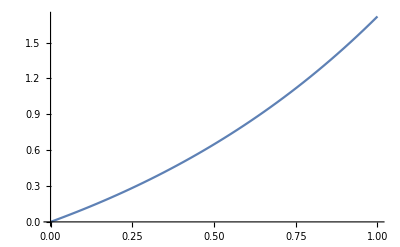
{0.09375,-Graphics-}

```mathematica
Plot[Sum[x^k/k!,{k,1,20}],{x,0,1}]//Timing (* 每当 plot 一个点的时候, 都会符号计算一遍 Sum[...], 然后再代入 x *)
```

```mathematica
Plot[Evaluate[Sum[x^k/k!,{k,1,20}]],{x,0,1}]//Timing (* Sum[...] 作为 argument 直接 evaluate了 (做了一次符号计算), 之后就不用重复做符号计算了 *)
```

{0.,-Graphics-}

还有一个 Head 叫做 Unevaluated, 它可以在不定义 Hold-attribute 的情况下, 临时地让一个函数的 argument 具有 hold-attribute like 的属性!

```mathematica
x = 7;
```

```mathematica
Head[x]
```

Integer

```mathematica
Head[Unevaluated[x]]
```

Symbol